```mathematica
ImportanceSampling[init_,genF_,accF_,samples_,burnIn_]:=
Module[{
samplesC=samples,
burnInC=burnIn,
states={},
state=init,
candidate},
While[samplesC>0,
candidate=genF[state];
While[Not[accF[candidate,state]],candidate=genF[state]];
AppendTo[states,candidate];
state=candidate;
If[burnInC>0,burnInC--,samplesC--]];
states];
```

```mathematica
Sampling[init_,genF_,accF_,samples_,burnIn_]:=
Module[{state=init,candidate=genF[init]},
(*去掉前面 burnIn 个采样点*)
Do[Until[accF[candidate,state],candidate=genF[state]],burnIn];state=candidate;
(*记录 samples 个采样点*)
Table[Until[accF[candidate,state],candidate=genF[state]];state=candidate,samples]];
```

## 一维随机

```mathematica
oneDU[state_]:=(state-3)^2*(state+10)^2;
oneDGen[state_]:=RandomReal[{-1,1}]+state;
oneDAcc[state2_,state1_]:=
With[{dE=oneDU[state2]-oneDU[state1],kT=300},
Or[dE<0,RandomReal[]<Exp[-dE/kT]]];
```

```mathematica
oneDat=Sampling[0,oneDGen,oneDAcc,100000,100];
```

```mathematica
Timing[Sampling[0,oneDGen,oneDAcc,100000,100];]
```

{0.888991,Null}

```mathematica
Timing[ImportanceSampling[0,oneDGen,oneDAcc,100000,100];]
```

{9.30457,Null}

```mathematica
pltU=Plot[(x-3)^2(x+10)^2,{x,-20,10}];
```

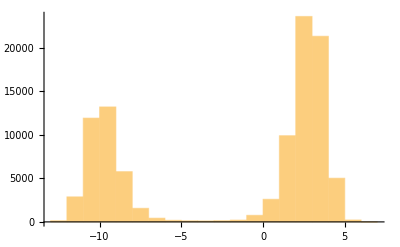

```mathematica
hist=Histogram[oneDat]
```

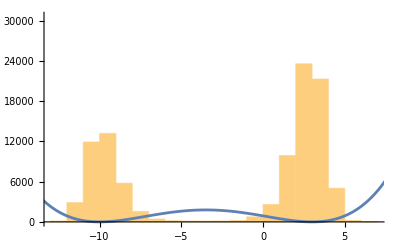

```mathematica
Show[{hist,pltU}]
```

```mathematica
oneDAni=Animate[Show[{
Histogram[oneDat[[;;t]]],
Graphics@{PointSize[0.02],Point[{oneDat[[t]],0}]}
}],{t,1,10000,1},AnimationRate->200]
```

```mathematica
Export["~/Buff/oneDAni.gif",oneDAni,"GIF"]
```

~/Buff/oneDAni.gif

```mathematica
dat=Flatten@Import["~/Buff/mc.test","CSV"];
```

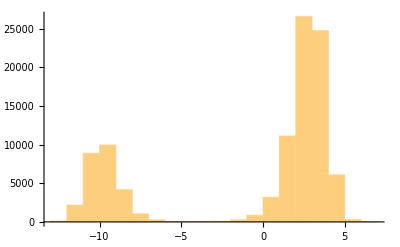

```mathematica
Histogram[dat]
```

## 二维随机

认为 state 是一个二维向量, 对于自由行走:

```mathematica
twoDU[state_]:=0;
twoDGen[state_]:=With[{vec=Table[RandomReal[{-1,1}],2]},(If[Norm[vec]!=0,vec/Norm[vec],vec])+state];
twoDAcc[state2_,state1_]:=
With[{dE=twoDU[state2]-twoDU[state1],kT=300},
Or[dE<0,RandomReal[]<Exp[-dE/kT]]];
```

```mathematica
twoDat=Sampling[{0,0},twoDGen,twoDAcc,100000,100];
```

```mathematica
twoDAni=Animate[Show[{
DensityHistogram[twoDat[[;;t]]],
Graphics[{PointSize[0.05],Point[twoDat[[t]]],Line[twoDat[[;;t]]]}]}],{t,1,100000,100},
AnimationRate->1000,AnimationRunning->True]
```

## Ising Model